# xlr8r example

## Map-Kinase Cascade: Oscillations due to Negative Feedback

This notebook gives an example of self-sustaining oscillations that emerge from a 3-stage MAP kinase cascade due to negative feedback.  The output of the cascade (doubly phosphorylated MAPK, Kpp in the model) noncompetitively inhibits the first stage of phosphorylation,.

Reference 
[1] Kholodenko, Boris N. Eur J Biochem 267:1583-8 (2000) "Negative feedback and ultrasensitivity can bring about oscillations in the mitogen-activated protein kinase cascades"

xCellerator implementation
Created: 12-Aug-2005 BES
Revised: 15 Oct 2007 BES - verify under Mathematica v6.0

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 13:46:57.633219 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

### define Noncompetitive Inhibition wrapper for M-M equations (see Segel page 129, for example)

```mathematica
NCI[MM[K_, V_], Inh_, KI_]:= MM[K, V/(1+Inh/KI)];
```

### define the signal transduction network

#### Note: the variable "K" is not used because of potential collision with the Elliptic Integral of the First Kind K[t] in Mathematica.

```mathematica
stn={

(* phosphorylation reactions *) 
(* Non-competitive inhibition of first stage of cascade by Kpp (MAPK-pp)  *)

{KKK⟹KKKp,NCI[MM[K1,V1], Kpp[t], KI]},
{Overscript[KK⟹KKp, KKKp],MM[K3,k3]},{Overscript[KKp⟹KKpp, KKKp],MM[K4,k4]},
{Overscript[MAPK⟹Kp, KKpp],MM[K7,k7]},{Overscript[Kp⟹Kpp, KKpp],MM[K8,k8]},

(* dephosphorylation reactions *) 

{KKKp⟹KKK, MM[K2,V2]},
{KKpp⟹KKp, MM[K5,V5]},{KKp⟹KK, MM[K6,V6]},
{Kpp⟹Kp, MM[K9,V9]},{Kp⟹MAPK, MM[K10,V10]}

};
```

```mathematica
interpret[stn]
```

{{KK'[t]==-(k3 KK[t] KKKp[t])/(K3+KK[t])+(V6 KKp[t])/(K6+KKp[t]),KKK'[t]==(V2 KKKp[t])/(K2+KKKp[t])-(V1 KKK[t])/((K1+KKK[t]) (1+Kpp[t]/KI)),KKKp'[t]==-(V2 KKKp[t])/(K2+KKKp[t])+(V1 KKK[t])/((K1+KKK[t]) (1+Kpp[t]/KI)),KKp'[t]==(k3 KK[t] KKKp[t])/(K3+KK[t])-(k4 KKKp[t] KKp[t])/(K4+KKp[t])-(V6 KKp[t])/(K6+KKp[t])+(V5 KKpp[t])/(K5+KKpp[t]),KKpp'[t]==(k4 KKKp[t] KKp[t])/(K4+KKp[t])-(V5 KKpp[t])/(K5+KKpp[t]),Kp'[t]==-(V10 Kp[t])/(K10+Kp[t])-(k8 KKpp[t] Kp[t])/(K8+Kp[t])+(V9 Kpp[t])/(K9+Kpp[t])+(k7 KKpp[t] MAPK[t])/(K7+MAPK[t]),Kpp'[t]==(k8 KKpp[t] Kp[t])/(K8+Kp[t])-(V9 Kpp[t])/(K9+Kpp[t]),MAPK'[t]==(V10 Kp[t])/(K10+Kp[t])-(k7 KKpp[t] MAPK[t])/(K7+MAPK[t])},{KK,KKK,KKKp,KKp,KKpp,Kp,Kpp,MAPK}}

### rate constants are based on Table 2 reference [1].

```mathematica
r={V1-> 2.5, V2-> 0.25,k3-> 0.025, k4-> 0.025, V5-> 0.75, V6-> 0.75,k7-> 0.025, k8-> 0.025,V9-> 0.5, V10-> 0.5, K1-> 10, K2-> 8, K3-> 15, K4-> 15, K5-> 15, K6-> 15, K7-> 15, K8-> 15, K9-> 15, K10-> 15, KI-> 10};
```

### define initial conditions

```mathematica
myic={KKK-> 100,KKKp-> 0, KK-> 300, KKp-> 0, KKpp-> 0, MAPK-> 300, Kp-> 0, Kpp-> 0}
```

{KKK→100,KKKp→0,KK→300,KKp→0,KKpp→0,MAPK→300,Kp→0,Kpp→0}

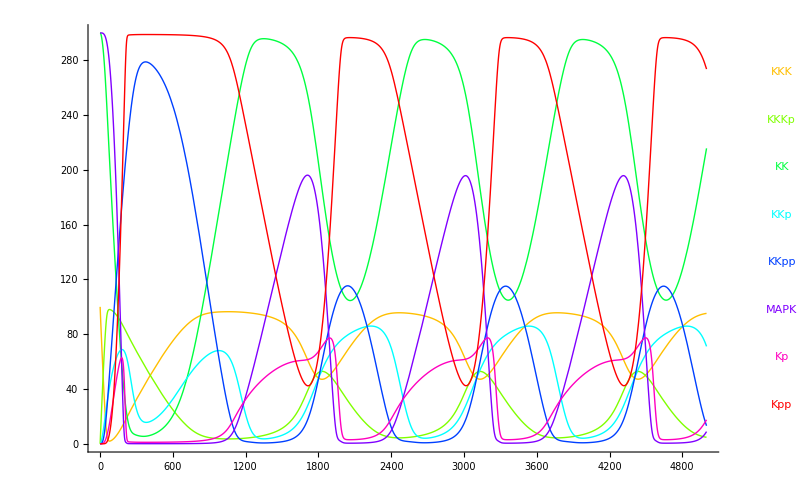

{{KK→InterpolatingFunction[{{0.,5000.}},<>],KKK→InterpolatingFunction[{{0.,5000.}},<>],KKKp→InterpolatingFunction[{{0.,5000.}},<>],KKp→InterpolatingFunction[{{0.,5000.}},<>],KKpp→InterpolatingFunction[{{0.,5000.}},<>],Kp→InterpolatingFunction[{{0.,5000.}},<>],Kpp→InterpolatingFunction[{{0.,5000.}},<>],MAPK→InterpolatingFunction[{{0.,5000.}},<>]}}

```mathematica
sim=run[stn/.r,initialConditions-> myic,timeSpan-> {0,5000},   plotVariables-> {KKK, KKKp, KK, KKp, KKpp, MAPK, Kp, Kpp}, plot-> True, ImageSize-> 800]
```